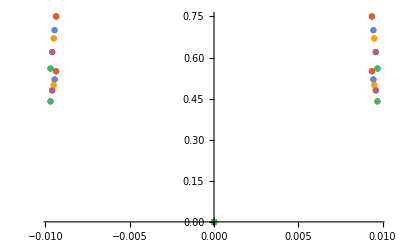

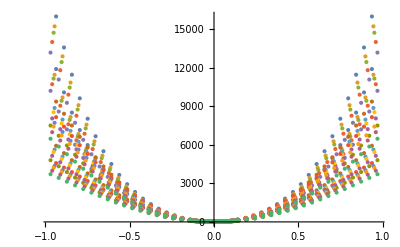

```mathematica
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,15}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,15}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,15}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,15}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
```

```mathematica
(*Solve carbon harmonic and anharmonic, first vol, 001 direction*)
ℒallch=Table[-(1/(2m[[1]]))*u''[x]+V[1,2,x][[1]]*u[x],{i,1,1}];
ℒallca=Table[-(1/(2m[[1]]))*u''[x]+V[1,6,x][[1]]*u[x],{i,1,1}];
(*Solve carbon harmonic and anharmonic, first vol, 001 direction*)
ℒallzh=Table[-(1/(2m[[1]]))*u''[x]+V[2,2,x][[1]]*u[x],{i,1,1}];
ℒallza=Table[-(1/(2m[[1]]))*u''[x]+V[2,6,x][[1]]*u[x],{i,1,1}];
```

```mathematica
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=100;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Solveroptions*)
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

```mathematica
(*Solve eigensystems*)
eigensysch=Table[NDEigensystem[ℒallch,u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
eigensysca=Table[NDEigensystem[ℒallca[[1]][[j]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
eigensyszh=Table[NDEigensystem[ℒallzh,u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
eigensysza=Table[NDEigensystem[ℒallza[[1]][[j]],u[x],{x
,-B,B},Neigenvalues,Evaluate@solverOptions],{j,1,1}];
```

```mathematica
charval=eigensysch[[1]][[1]][[1;;100]];
charvec=eigensysch[[1]][[2]][[1;;100]];
```

```mathematica
(*Occupation functions - partition and Bose-Einstein*)
Z[eval_,T_]:=N[Sum[Exp[-eval[[i]]/(K2meV*T)],{i,1,Length[eval]}],20]
n[eval_,T_]:=1/(Exp[(eval)/(kB*T)]-1)

(*Density matrices*)

denMatKernal[eval_,evec_,T_]:=Sum[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}]
denMatKernalExpect[kernel_,eval_,T_]:=(1/Z[eval,T])*NIntegrate[kernel,{x,-0.7,0.7}]

densMatSpectrum[O_,eval_,evec_,T_]:=(1/Z[eval,T])*O*Table[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}]

densMatOperator[O_,eval_,evec_,T_]:=(1/Z[eval,T])*O*Sum[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}]

densMatExpect[O_,eval_,evec_,T_]:=(1/Z[eval,T])*NIntegrate[O*Sum[Exp[-eval[[i]]/(K2meV*T)]*evec[[i]]*evec[[i]],{i,1,Length[eval]}],{x,-0.7,0.7}]
```

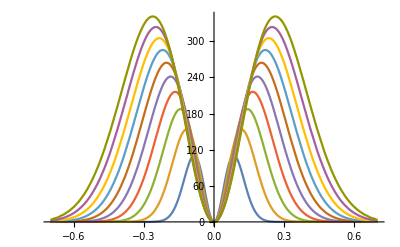

-Graphics-

22.5428
43.5899
64.9659
86.4254
107.918
129.421
150.907
172.321
193.577
214.567

```mathematica
(*carbon Potential V[X] expectation*)
Plot[Evaluate@Table[densMatOperator[Evaluate@V[1,2,x][[1]],charval,charvec,500*i],{i,1,10}],{x,-0.7,0.7},PlotRange->All]

Plot[Evaluate@densMatSpectrum[Evaluate@V[1,2,x][[1]],charval,charvec,1000],{x,-0.7,0.7},PlotRange->All]

Table[densMatExpect[Evaluate@V[1,2,x][[1]],charval,charvec,500*i],{i,1,10}]//TableForm
```

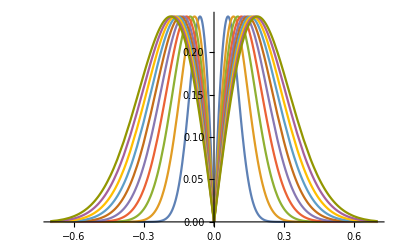

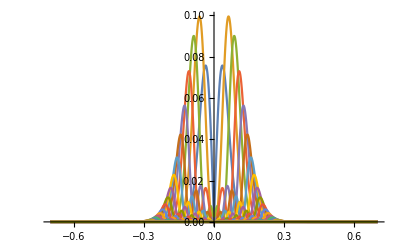

0.0478632
0.0665566
0.0812533
0.0937171
0.104724
0.114685
0.123846
0.132358
0.140321
0.147795

```mathematica
(*position x expectation*)
Plot[Evaluate@Table[densMatOperator[Norm@x,charval,charvec,500*i],{i,1,10}],{x,-0.7,0.7},PlotRange->All]

Plot[Evaluate@densMatSpectrum[Norm@x,charval,charvec,1000],{x,-0.7,0.7},PlotRange->All]

Table[densMatExpect[Norm@x,charval,charvec,500*i],{i,1,10}]//TableForm
```

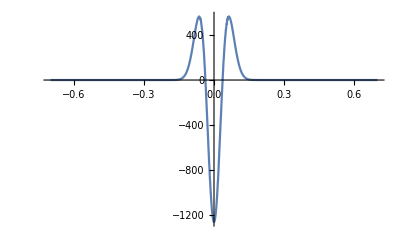

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0683811}. NIntegrate obtained 0.291867 and 0.388532 for the integral and error estimates.

0.223942

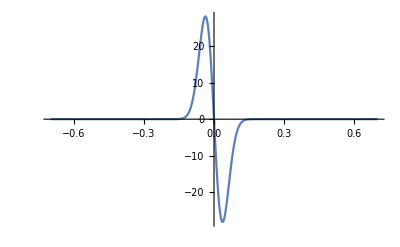

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0574436}. NIntegrate obtained -1.37501×10^-13 and 0.0000361211 for the integral and error estimates.

-1.05501×10^-13

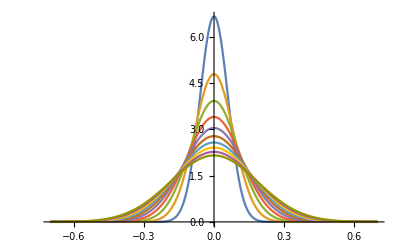

1.

```mathematica
(*kinetic d2/dx2*)
Plot[Evaluate@D[denMatKernal[charval,charvec,100],{x,2}],{x,-0.7,0.7},PlotRange->All]
denMatKernalExpect[Evaluate@D[denMatKernal[charval,charvec,500],{x,2}],charval,500]
(*momentum d2/dx2*)
Plot[Evaluate@D[denMatKernal[charval,charvec,100],{x,1}],{x,-0.7,0.7},PlotRange->All]
denMatKernalExpect[Evaluate@D[denMatKernal[charval,charvec,500],{x,1}],charval,500]
```

```mathematica
(*Unit operator , 1*)
Plot[Evaluate@Table[densMatOperator[1,charval,charvec,500*i],{i,1,10}],{x,-0.7,0.7},PlotRange->All]
densMatExpect[1,charval,charvec,2000]
Plot[Evaluate@densMatSpectrum[1,charval,charvec,5000],{x,-0.7,0.7},PlotRange->All]
Plot[Evaluate@Table[densMatOp[1,charval,charvec,500*i],{i,1,10}],{x,-0.7,0.7},PlotRange->All]
```

-Graphics-

1.

-Graphics-

-Graphics-

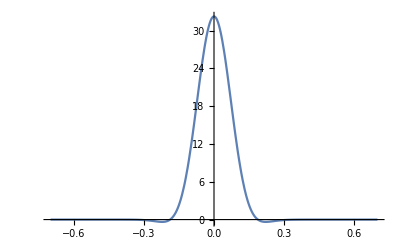

1.12121

```mathematica
(*Entropy*)
Plot[Evaluate@denMatKernal[charval,charvec,1000]*Log[denMatKernal[charval,charvec,1000]],{x,-0.7,0.7},PlotRange->All]
denMatKernalExpect[Evaluate@denMatKernal[charval,charvec,500]*Log[denMatKernal[charval,charvec,1000]],charval,1000]
```